```mathematica
a={1,2,4,8};
p[x_,a_]:=Boole[Abs[x]<=a]/(2a)
b=10;
```

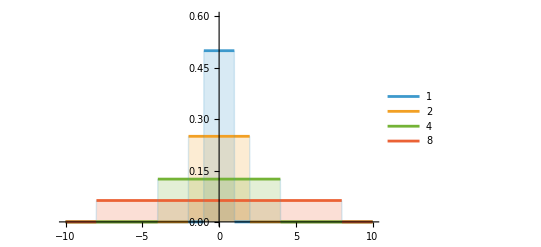

```mathematica
Plot[Evaluate[Table[p[x,c],{c,a}]],
{x,-b,b},
Filling->Bottom,
PlotLegends->a,
PlotRange->{Full,{0,1/(2*a[[1]])+0.1}}]
```